```mathematica
ClearAll;
k = 1.0;
Oscillator = NDSolve[{s'[t] == v[t],v'[t] == -k* s[t], s[0]==1.0,v[0]==0.0 },{s[t],v[t]}, {t,0,10}]
```

{{s[t]→InterpolatingFunction[{{0., 10.}}, <>][t],v[t]→InterpolatingFunction[{{0., 10.}}, <>][t]}}

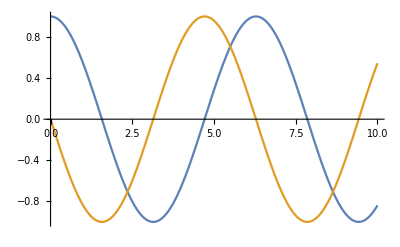

```mathematica
Plot[Evaluate[{s[t],v[t]} /. Oscillator], {t,0,10}, PlotRange -> All, PlotPoints-> 3000]
```

```mathematica
ClearAll;
k = 1.0;
q=10*6.28;
w = 6.28 * 0.10;
OscillatorEuler = NDSolve[{s'[t] == v[t],v'[t] == -k* s[t], s[0]==1.0,v[0]==0.0 },{s[t],v[t]}, {t,0,q}, StartingStepSize -> w, Method -> {"FixedStep", Method -> "ExplicitEuler"}]
```

{{s[t]→InterpolatingFunction[{{0., 62.8}}, <>][t],v[t]→InterpolatingFunction[{{0., 62.8}}, <>][t]}}

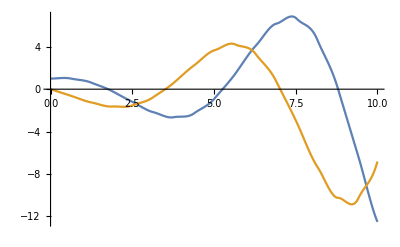

```mathematica
Plot[Evaluate[{s[t],v[t]} /. OscillatorEuler], {t,0,10}, PlotRange -> All, PlotPoints-> 3000]
```

```mathematica
ClearAll;
k = 1.0;
q=10*6.28;
w = 6.28 * 0.05;
OscillatorEuler2 = NDSolve[{s'[t] == v[t],v'[t] == -k* s[t], s[0]==1.0,v[0]==0.0 },{s[t],v[t]}, {t,0,q}, StartingStepSize -> w, Method -> {"FixedStep", Method -> "ExplicitEuler"}]
```

{{s[t]→InterpolatingFunction[{{0., 62.8}}, <>][t],v[t]→InterpolatingFunction[{{0., 62.8}}, <>][t]}}

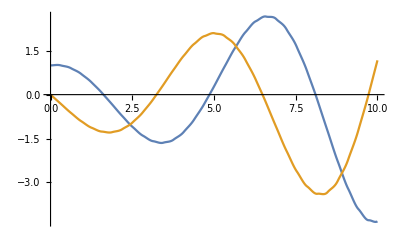

```mathematica
Plot[Evaluate[{s[t],v[t]} /. OscillatorEuler2], {t,0,10}, PlotRange -> All, PlotPoints-> 3000]
```

```mathematica
ClearAll;
k = 1.0;
q=10*6.28;
w = 6.28 * 0.10;
OscillatorRungeKutta = NDSolve[{s'[t] == v[t],v'[t] == -k* s[t], s[0]==1.0,v[0]==0.0 },{s[t],v[t]}, {t,0,q}, StartingStepSize -> w, Method -> {"FixedStep", Method -> {"ExplicitRungeKutta", "DifferenceOrder" -> 2}}]
```

{{s[t]→InterpolatingFunction[{{0., 62.8}}, <>][t],v[t]→InterpolatingFunction[{{0., 62.8}}, <>][t]}}

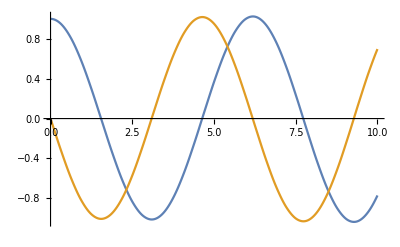

```mathematica
Plot[Evaluate[{s[t],v[t]} /. OscillatorRungeKutta], {t,0,10}, PlotRange -> All, PlotPoints-> 3000]
```

```mathematica
ClearAll;
k = 1.0;
q=10*6.28;
w = 6.28 * 0.05;
OscillatorRungeKutta2 = NDSolve[{s'[t] == v[t],v'[t] == -k* s[t], s[0]==1.0,v[0]==0.0 },{s[t],v[t]}, {t,0,q}, StartingStepSize -> w, Method -> {"FixedStep", Method -> {"ExplicitRungeKutta", "DifferenceOrder" -> 2}}]
```

{{s[t]→InterpolatingFunction[{{0., 62.8}}, <>][t],v[t]→InterpolatingFunction[{{0., 62.8}}, <>][t]}}

```mathematica
Plot[Evaluate[{s[t],v[t]} /. OscillatorRungeKutta2], {t,0,10}, PlotRange -> All, PlotPoints-> 3000]
```

-Graphics-

```mathematica
ClearAll;
k = 1.0;
q=10*6.28;
w = 6.28 * 0.10;
OscillatorRungeKutta3 = NDSolve[{s'[t] == v[t],v'[t] == -k* s[t], s[0]==1.0,v[0]==0.0 },{s[t],v[t]}, {t,0,q}, StartingStepSize -> w, Method -> {"FixedStep", Method -> {"ExplicitRungeKutta", "DifferenceOrder" -> 4}}]
```

{{s[t]→InterpolatingFunction[{{0., 62.8}}, <>][t],v[t]→InterpolatingFunction[{{0., 62.8}}, <>][t]}}

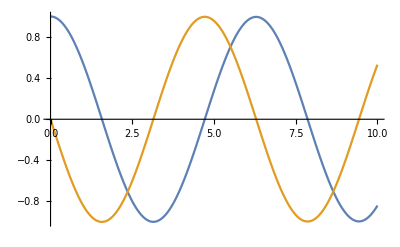

```mathematica
Plot[Evaluate[{s[t],v[t]} /. OscillatorRungeKutta3], {t,0,10}, PlotRange -> All, PlotPoints-> 3000]
```

```mathematica
ClearAll;
k = 1.0;
q=10*6.28;
w = 6.28 * 0.05;
OscillatorRungeKutta4 = NDSolve[{s'[t] == v[t],v'[t] == -k* s[t], s[0]==1.0,v[0]==0.0 },{s[t],v[t]}, {t,0,q}, StartingStepSize -> w, Method -> {"FixedStep", Method -> {"ExplicitRungeKutta", "DifferenceOrder" -> 4}}]
```

{{s[t]→InterpolatingFunction[{{0., 62.8}}, <>][t],v[t]→InterpolatingFunction[{{0., 62.8}}, <>][t]}}

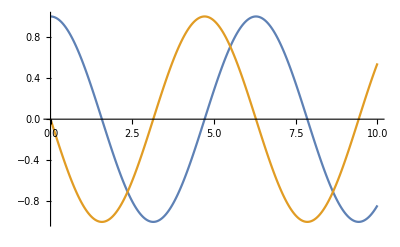

```mathematica
Plot[Evaluate[{s[t],v[t]} /. OscillatorRungeKutta4], {t,0,10}, PlotRange -> All, PlotPoints-> 3000]
```